# px5503 - Data Visualisation 6 - Focusing the viewer’s attention

Even after you cleaned up your graph and are left with no visual distractions, some parts of the plot are more important than others, and you want to draw the eyes of your audience to those parts. Consider for example this plot:

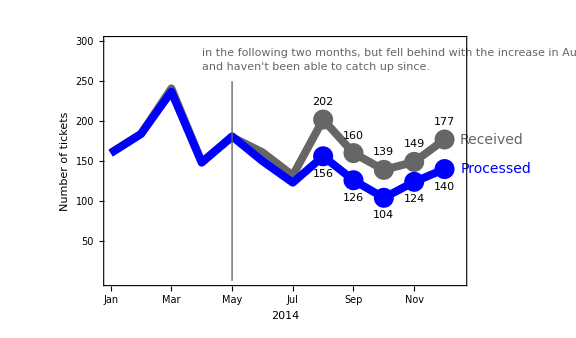

Without being told to do so, your eyes automatically drift towards the line depicting processed tickets, and then towards the right-hand side of the plot. This is not fortuitous: the right-hand side of the plot is where most of this graph’s story happens, and is where the main point is best illustrated.

In this section we will learn how to highlight parts of a graph and de-emphasise others, by making choosing carefully what to show and how to show it.

## Principles of visual perception: pre-attentive attributes

Certain visual cues attract our attention instinctively, without any conscious thought; these visual properties are called pre-attentive attributes. To illustrate them, try to count how many times the letter a appears in the following text:

We shall fight in France, we shall fight on the seas and oceans...

Now try again, with a slight change in the way we show the text:

We shall fight in France, we shall fight on the seas and oceans...

Just by changing the colour of the a’s to solid black, the contrast to the faded gray of the other letters makes them pop up in our vision without any effort on our part. We use this all the time in text; in fact, I just used it in the previous sentence! Boldface, italics, underlined, ... these are all ways to use pre-attentive attributes to focus the reader’s attention on the parts of the text we consider most important.

In order to learn how to do the same thing with graphs and visualisations, we first need to know what are the pre-attentive attributes.

### Colour

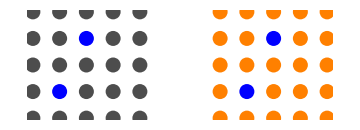

Colour is a strong pre-attentive attribute. An object with a strong colour placed among colourless objects immediately attracts the eyes. For that reason, making most of your plot gray and using a colour to indicate the most important parts is a very effective way to use highlighting in your visuals. In this example:

Blue is the only colour used in this plot, so our eyes are immediately attracted to the blue curve. This is what we want here, because the story we are telling revolves around the number of processed tickets and how it suffered after the departures in May of two people. The “received” curve is there to support this story, by comparing what we do with what we need to do; but it is not the main focus of the plot, so it is rendered in dark gray. Everything else is also rendered in gray, so everything else fades into the background when we look at this image. 

The use of colour here is a deliberate choice, based on what we decide to highlight or de-emphasise. Colour (and the other attributes) should always be used like that, otherwise our audience will not get what we are saying, and will be looking at the wrong thing. Here is an example of misusing colour:

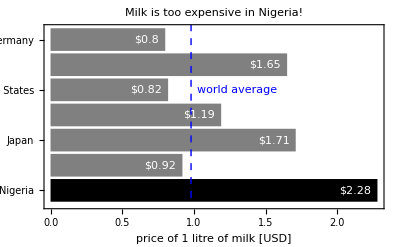

Our eyes are naturally attracted to the only coloured feature in the plot, namely the line indicating the average price. This competes with the highlighting of Nigeria, which should be the focus of this graph. 

The lesson from the previous examples is clear: colour is a very powerful way to focus attention, and should be used sparingly and deliberately. If misused, colour will call attention to the wrong things, and becomes a distraction.

A colour will also stand out among objects of another colour. This is effect is usually not as strong as when the other objects are colourless, however, and it is weaker the more colours there are. To illustrate, look at this:

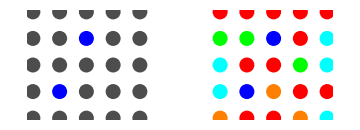

Now the two blue dots are lost in a sea of colours, and the highlighting effects of colours are gone. To be effective, colour should be used sparingly. The vast majority of plots should have only two or three colours. There are exceptions, but they are very few. Here is an example of using colours with wild abandon:

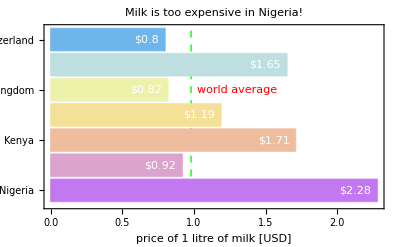

#### Tone

In addition to focusing our attention, colours can set the mood (that is, the tone) of a visual. For example, red is often associated with anger, violence, danger; light blue suggests feelings of tranquility and happiness; and a black and white plot often comes across as frugal, sensible, down to earth. You may want to use different colours to match the appropriate tone for the subject matter. Compare these two versions of the same plot:

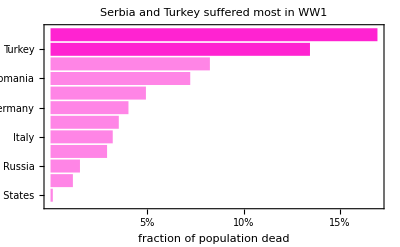

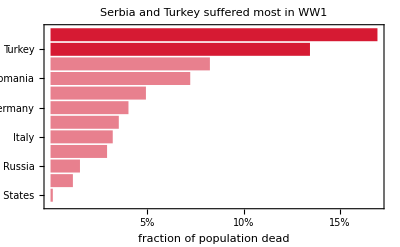

#### Colour blindness

About 8% of men and under 1% of women are colour-blind. This is a significant fraction of your audience, and you should design your visuals with that in mind. Most people affected by colour blindness have trouble differentiating red from green, so avoid using those two colours on the same plot. Red and green are the colours used in traffic light, and they are often used to contrast positive and negative feelings, such as danger (red) versus safety (green). Orange and Blue are a pair of colours that evoke those same feelings but do not cause problems for most colour-blind people.

### Intensity

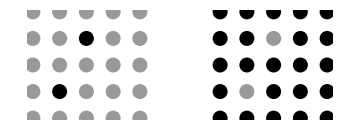

Our eyes are attracted to intense colours, versus faded ones. So we notice immediately the two dots on the left. Our eyes will tend to rest on shapes with intense colours even when the majority of the shapes are intense.  On the pattern to the right, our eyes will roam from dark dot to dark dot; the gray dots are felt as an absence, but are not highlighted. This is why intense colours should always be used to highlight the most relevant parts of your visuals; you should never use faded colours for that.

Here is an example of using intensity to highlight the most relevant parts of a black-and-white plot:

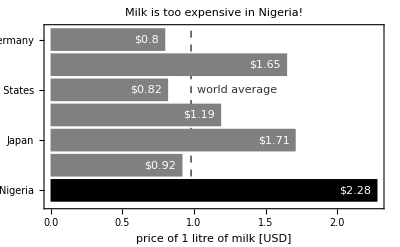

And here is an example with colours:

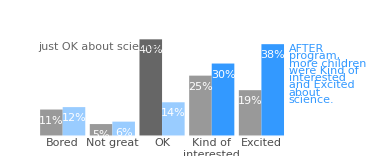

### Size

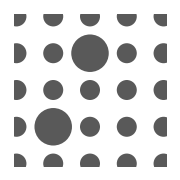

We notice the two big dots right away. The size pre-attentive attribute is relevant to every bar chart, because we perceive the bars as solid objects, and their size stands for the quantity they represent. This means that our attention will tend to focus on the higher bars first. This should be taken into account when deciding if you want to use a bar chart. They are often a good choice if the quantity or quantities you want to focus on are the largest in the data set.

This is used, along with other attributes such as colour and intensity, to call attention to the “OK” gray bar in the centre, and the “Excited” blue bar at the end:

### Extra features

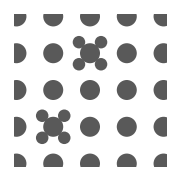

Parts of a graph that are “busier”, that is, that have more markers and more features, tend to attract our attention more than parts that are “calmer”. This is one of the reasons why we should delete spurious features: they may unintentionally focus our audience’s attention on the wrong spots. We can, however, harness this principle for our benefit. This is done in this example:

The point markers, the point labels and the data labels all draw our eyes to the right side of this plot, which is where the main story is told, and where the main point is made. Also notice that the text on the top is placed to that most of it is lying to the right of the vertical line that indicates the month of May; this also contributes to making the right-hand side busy. This is further helped by the fact that the two lines lie on top of each other before May, and their bifurcation after May is yet another way in which this side of the plot has more going on.

### Line thickness

The final pre-attentive attribute we will discuss is line thickness. Thicker lines are emphasised compared to thin lines. In this example:

The two lines representing the data are plotted as thick lines, and all other lines - the axes, the ticks marks, and the vertical line indicating May - are much thinner. This has the effect of highlighting the data compared to those other features, which are there to help us understand the data being shown, but should not compete with it for attention.

### Other attributes

There are other pre-attentive attributes, such as orientation and curvature, but we will not cover them, because they are used in most graphs less frequently than the ones we have discussed above.

## Example

Compare this version:

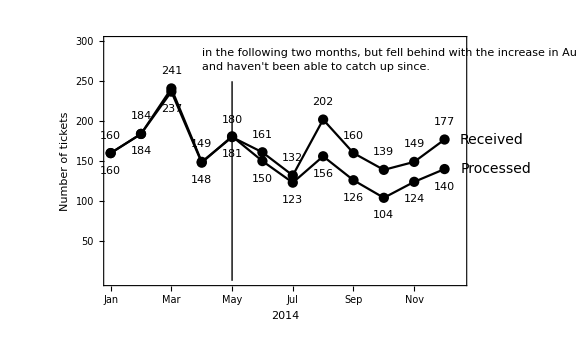

... or this version:

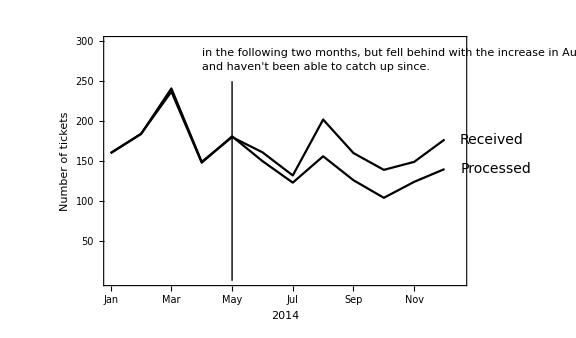

This last version is clean: it does not have visual distractions. But no emphasis is placed anywhere. In particular, the lines representing the data do not stand out from other features such as the axes, or the text. When I look at this plot, my eyes keep wandering, not knowing where to rest. Compare this with this version of the plot, where we use the pre-attentive attributes to focus attention in the right way:

## Challenge

The following cell defines variables containing data on the average world temperature from 1880 to the present day.

```mathematica
dates = {1880.04,1880.13,1880.21,1880.29,1880.38,1880.46,1880.54,1880.63,1880.71,1880.79,1880.88,1880.96,1881.04,1881.13,1881.21,1881.29,1881.38,1881.46,1881.54,1881.63,1881.71,1881.79,1881.88,1881.96,1882.04,1882.13,1882.21,1882.29,1882.38,1882.46,1882.54,1882.63,1882.71,1882.79,1882.88,1882.96,1883.04,1883.13,1883.21,1883.29,1883.38,1883.46,1883.54,1883.63,1883.71,1883.79,1883.88,1883.96,1884.04,1884.13,1884.21,1884.29,1884.38,1884.46,1884.54,1884.63,1884.71,1884.79,1884.88,1884.96,1885.04,1885.13,1885.21,1885.29,1885.38,1885.46,1885.54,1885.63,1885.71,1885.79,1885.88,1885.96,1886.04,1886.13,1886.21,1886.29,1886.38,1886.46,1886.54,1886.63,1886.71,1886.79,1886.88,1886.96,1887.04,1887.13,1887.21,1887.29,1887.38,1887.46,1887.54,1887.63,1887.71,1887.79,1887.88,1887.96,1888.04,1888.13,1888.21,1888.29,1888.38,1888.46,1888.54,1888.63,1888.71,1888.79,1888.88,1888.96,1889.04,1889.13,1889.21,1889.29,1889.38,1889.46,1889.54,1889.63,1889.71,1889.79,1889.88,1889.96,1890.04,1890.13,1890.21,1890.29,1890.38,1890.46,1890.54,1890.63,1890.71,1890.79,1890.88,1890.96,1891.04,1891.13,1891.21,1891.29,1891.38,1891.46,1891.54,1891.63,1891.71,1891.79,1891.88,1891.96,1892.04,1892.13,1892.21,1892.29,1892.38,1892.46,1892.54,1892.63,1892.71,1892.79,1892.88,1892.96,1893.04,1893.13,1893.21,1893.29,1893.38,1893.46,1893.54,1893.63,1893.71,1893.79,1893.88,1893.96,1894.04,1894.13,1894.21,1894.29,1894.38,1894.46,1894.54,1894.63,1894.71,1894.79,1894.88,1894.96,1895.04,1895.13,1895.21,1895.29,1895.38,1895.46,1895.54,1895.63,1895.71,1895.79,1895.88,1895.96,1896.04,1896.13,1896.21,1896.29,1896.38,1896.46,1896.54,1896.63,1896.71,1896.79,1896.88,1896.96,1897.04,1897.13,1897.21,1897.29,1897.38,1897.46,1897.54,1897.63,1897.71,1897.79,1897.88,1897.96,1898.04,1898.13,1898.21,1898.29,1898.38,1898.46,1898.54,1898.63,1898.71,1898.79,1898.88,1898.96,1899.04,1899.13,1899.21,1899.29,1899.38,1899.46,1899.54,1899.63,1899.71,1899.79,1899.88,1899.96,1900.04,1900.13,1900.21,1900.29,1900.38,1900.46,1900.54,1900.63,1900.71,1900.79,1900.88,1900.96,1901.04,1901.13,1901.21,1901.29,1901.38,1901.46,1901.54,1901.63,1901.71,1901.79,1901.88,1901.96,1902.04,1902.13,1902.21,1902.29,1902.38,1902.46,1902.54,1902.63,1902.71,1902.79,1902.88,1902.96,1903.04,1903.13,1903.21,1903.29,1903.38,1903.46,1903.54,1903.63,1903.71,1903.79,1903.88,1903.96,1904.04,1904.13,1904.21,1904.29,1904.38,1904.46,1904.54,1904.63,1904.71,1904.79,1904.88,1904.96,1905.04,1905.13,1905.21,1905.29,1905.38,1905.46,1905.54,1905.63,1905.71,1905.79,1905.88,1905.96,1906.04,1906.13,1906.21,1906.29,1906.38,1906.46,1906.54,1906.63,1906.71,1906.79,1906.88,1906.96,1907.04,1907.13,1907.21,1907.29,1907.38,1907.46,1907.54,1907.63,1907.71,1907.79,1907.88,1907.96,1908.04,1908.13,1908.21,1908.29,1908.38,1908.46,1908.54,1908.63,1908.71,1908.79,1908.88,1908.96,1909.04,1909.13,1909.21,1909.29,1909.38,1909.46,1909.54,1909.63,1909.71,1909.79,1909.88,1909.96,1910.04,1910.13,1910.21,1910.29,1910.38,1910.46,1910.54,1910.63,1910.71,1910.79,1910.88,1910.96,1911.04,1911.13,1911.21,1911.29,1911.38,1911.46,1911.54,1911.63,1911.71,1911.79,1911.88,1911.96,1912.04,1912.13,1912.21,1912.29,1912.38,1912.46,1912.54,1912.63,1912.71,1912.79,1912.88,1912.96,1913.04,1913.13,1913.21,1913.29,1913.38,1913.46,1913.54,1913.63,1913.71,1913.79,1913.88,1913.96,1914.04,1914.13,1914.21,1914.29,1914.38,1914.46,1914.54,1914.63,1914.71,1914.79,1914.88,1914.96,1915.04,1915.13,1915.21,1915.29,1915.38,1915.46,1915.54,1915.63,1915.71,1915.79,1915.88,1915.96,1916.04,1916.13,1916.21,1916.29,1916.38,1916.46,1916.54,1916.63,1916.71,1916.79,1916.88,1916.96,1917.04,1917.13,1917.21,1917.29,1917.38,1917.46,1917.54,1917.63,1917.71,1917.79,1917.88,1917.96,1918.04,1918.13,1918.21,1918.29,1918.38,1918.46,1918.54,1918.63,1918.71,1918.79,1918.88,1918.96,1919.04,1919.13,1919.21,1919.29,1919.38,1919.46,1919.54,1919.63,1919.71,1919.79,1919.88,1919.96,1920.04,1920.13,1920.21,1920.29,1920.38,1920.46,1920.54,1920.63,1920.71,1920.79,1920.88,1920.96,1921.04,1921.13,1921.21,1921.29,1921.38,1921.46,1921.54,1921.63,1921.71,1921.79,1921.88,1921.96,1922.04,1922.13,1922.21,1922.29,1922.38,1922.46,1922.54,1922.63,1922.71,1922.79,1922.88,1922.96,1923.04,1923.13,1923.21,1923.29,1923.38,1923.46,1923.54,1923.63,1923.71,1923.79,1923.88,1923.96,1924.04,1924.13,1924.21,1924.29,1924.38,1924.46,1924.54,1924.63,1924.71,1924.79,1924.88,1924.96,1925.04,1925.13,1925.21,1925.29,1925.38,1925.46,1925.54,1925.63,1925.71,1925.79,1925.88,1925.96,1926.04,1926.13,1926.21,1926.29,1926.38,1926.46,1926.54,1926.63,1926.71,1926.79,1926.88,1926.96,1927.04,1927.13,1927.21,1927.29,1927.38,1927.46,1927.54,1927.63,1927.71,1927.79,1927.88,1927.96,1928.04,1928.13,1928.21,1928.29,1928.38,1928.46,1928.54,1928.63,1928.71,1928.79,1928.88,1928.96,1929.04,1929.13,1929.21,1929.29,1929.38,1929.46,1929.54,1929.63,1929.71,1929.79,1929.88,1929.96,1930.04,1930.13,1930.21,1930.29,1930.38,1930.46,1930.54,1930.63,1930.71,1930.79,1930.88,1930.96,1931.04,1931.13,1931.21,1931.29,1931.38,1931.46,1931.54,1931.63,1931.71,1931.79,1931.88,1931.96,1932.04,1932.13,1932.21,1932.29,1932.38,1932.46,1932.54,1932.63,1932.71,1932.79,1932.88,1932.96,1933.04,1933.13,1933.21,1933.29,1933.38,1933.46,1933.54,1933.63,1933.71,1933.79,1933.88,1933.96,1934.04,1934.13,1934.21,1934.29,1934.38,1934.46,1934.54,1934.63,1934.71,1934.79,1934.88,1934.96,1935.04,1935.13,1935.21,1935.29,1935.38,1935.46,1935.54,1935.63,1935.71,1935.79,1935.88,1935.96,1936.04,1936.13,1936.21,1936.29,1936.38,1936.46,1936.54,1936.63,1936.71,1936.79,1936.88,1936.96,1937.04,1937.13,1937.21,1937.29,1937.38,1937.46,1937.54,1937.63,1937.71,1937.79,1937.88,1937.96,1938.04,1938.13,1938.21,1938.29,1938.38,1938.46,1938.54,1938.63,1938.71,1938.79,1938.88,1938.96,1939.04,1939.13,1939.21,1939.29,1939.38,1939.46,1939.54,1939.63,1939.71,1939.79,1939.88,1939.96,1940.04,1940.13,1940.21,1940.29,1940.38,1940.46,1940.54,1940.63,1940.71,1940.79,1940.88,1940.96,1941.04,1941.13,1941.21,1941.29,1941.38,1941.46,1941.54,1941.63,1941.71,1941.79,1941.88,1941.96,1942.04,1942.13,1942.21,1942.29,1942.38,1942.46,1942.54,1942.63,1942.71,1942.79,1942.88,1942.96,1943.04,1943.13,1943.21,1943.29,1943.38,1943.46,1943.54,1943.63,1943.71,1943.79,1943.88,1943.96,1944.04,1944.13,1944.21,1944.29,1944.38,1944.46,1944.54,1944.63,1944.71,1944.79,1944.88,1944.96,1945.04,1945.13,1945.21,1945.29,1945.38,1945.46,1945.54,1945.63,1945.71,1945.79,1945.88,1945.96,1946.04,1946.13,1946.21,1946.29,1946.38,1946.46,1946.54,1946.63,1946.71,1946.79,1946.88,1946.96,1947.04,1947.13,1947.21,1947.29,1947.38,1947.46,1947.54,1947.63,1947.71,1947.79,1947.88,1947.96,1948.04,1948.13,1948.21,1948.29,1948.38,1948.46,1948.54,1948.63,1948.71,1948.79,1948.88,1948.96,1949.04,1949.13,1949.21,1949.29,1949.38,1949.46,1949.54,1949.63,1949.71,1949.79,1949.88,1949.96,1950.04,1950.13,1950.21,1950.29,1950.38,1950.46,1950.54,1950.63,1950.71,1950.79,1950.88,1950.96,1951.04,1951.13,1951.21,1951.29,1951.38,1951.46,1951.54,1951.63,1951.71,1951.79,1951.88,1951.96,1952.04,1952.13,1952.21,1952.29,1952.38,1952.46,1952.54,1952.63,1952.71,1952.79,1952.88,1952.96,1953.04,1953.13,1953.21,1953.29,1953.38,1953.46,1953.54,1953.63,1953.71,1953.79,1953.88,1953.96,1954.04,1954.13,1954.21,1954.29,1954.38,1954.46,1954.54,1954.63,1954.71,1954.79,1954.88,1954.96,1955.04,1955.13,1955.21,1955.29,1955.38,1955.46,1955.54,1955.63,1955.71,1955.79,1955.88,1955.96,1956.04,1956.13,1956.21,1956.29,1956.38,1956.46,1956.54,1956.63,1956.71,1956.79,1956.88,1956.96,1957.04,1957.13,1957.21,1957.29,1957.38,1957.46,1957.54,1957.63,1957.71,1957.79,1957.88,1957.96,1958.04,1958.13,1958.21,1958.29,1958.38,1958.46,1958.54,1958.63,1958.71,1958.79,1958.88,1958.96,1959.04,1959.13,1959.21,1959.29,1959.38,1959.46,1959.54,1959.63,1959.71,1959.79,1959.88,1959.96,1960.04,1960.13,1960.21,1960.29,1960.38,1960.46,1960.54,1960.63,1960.71,1960.79,1960.88,1960.96,1961.04,1961.13,1961.21,1961.29,1961.38,1961.46,1961.54,1961.63,1961.71,1961.79,1961.88,1961.96,1962.04,1962.13,1962.21,1962.29,1962.38,1962.46,1962.54,1962.63,1962.71,1962.79,1962.88,1962.96,1963.04,1963.13,1963.21,1963.29,1963.38,1963.46,1963.54,1963.63,1963.71,1963.79,1963.88,1963.96,1964.04,1964.13,1964.21,1964.29,1964.38,1964.46,1964.54,1964.63,1964.71,1964.79,1964.88,1964.96,1965.04,1965.13,1965.21,1965.29,1965.38,1965.46,1965.54,1965.63,1965.71,1965.79,1965.88,1965.96,1966.04,1966.13,1966.21,1966.29,1966.38,1966.46,1966.54,1966.63,1966.71,1966.79,1966.88,1966.96,1967.04,1967.13,1967.21,1967.29,1967.38,1967.46,1967.54,1967.63,1967.71,1967.79,1967.88,1967.96,1968.04,1968.13,1968.21,1968.29,1968.38,1968.46,1968.54,1968.63,1968.71,1968.79,1968.88,1968.96,1969.04,1969.13,1969.21,1969.29,1969.38,1969.46,1969.54,1969.63,1969.71,1969.79,1969.88,1969.96,1970.04,1970.13,1970.21,1970.29,1970.38,1970.46,1970.54,1970.63,1970.71,1970.79,1970.88,1970.96,1971.04,1971.13,1971.21,1971.29,1971.38,1971.46,1971.54,1971.63,1971.71,1971.79,1971.88,1971.96,1972.04,1972.13,1972.21,1972.29,1972.38,1972.46,1972.54,1972.63,1972.71,1972.79,1972.88,1972.96,1973.04,1973.13,1973.21,1973.29,1973.38,1973.46,1973.54,1973.63,1973.71,1973.79,1973.88,1973.96,1974.04,1974.13,1974.21,1974.29,1974.38,1974.46,1974.54,1974.63,1974.71,1974.79,1974.88,1974.96,1975.04,1975.13,1975.21,1975.29,1975.38,1975.46,1975.54,1975.63,1975.71,1975.79,1975.88,1975.96,1976.04,1976.13,1976.21,1976.29,1976.38,1976.46,1976.54,1976.63,1976.71,1976.79,1976.88,1976.96,1977.04,1977.13,1977.21,1977.29,1977.38,1977.46,1977.54,1977.63,1977.71,1977.79,1977.88,1977.96,1978.04,1978.13,1978.21,1978.29,1978.38,1978.46,1978.54,1978.63,1978.71,1978.79,1978.88,1978.96,1979.04,1979.13,1979.21,1979.29,1979.38,1979.46,1979.54,1979.63,1979.71,1979.79,1979.88,1979.96,1980.04,1980.13,1980.21,1980.29,1980.38,1980.46,1980.54,1980.63,1980.71,1980.79,1980.88,1980.96,1981.04,1981.13,1981.21,1981.29,1981.38,1981.46,1981.54,1981.63,1981.71,1981.79,1981.88,1981.96,1982.04,1982.13,1982.21,1982.29,1982.38,1982.46,1982.54,1982.63,1982.71,1982.79,1982.88,1982.96,1983.04,1983.13,1983.21,1983.29,1983.38,1983.46,1983.54,1983.63,1983.71,1983.79,1983.88,1983.96,1984.04,1984.13,1984.21,1984.29,1984.38,1984.46,1984.54,1984.63,1984.71,1984.79,1984.88,1984.96,1985.04,1985.13,1985.21,1985.29,1985.38,1985.46,1985.54,1985.63,1985.71,1985.79,1985.88,1985.96,1986.04,1986.13,1986.21,1986.29,1986.38,1986.46,1986.54,1986.63,1986.71,1986.79,1986.88,1986.96,1987.04,1987.13,1987.21,1987.29,1987.38,1987.46,1987.54,1987.63,1987.71,1987.79,1987.88,1987.96,1988.04,1988.13,1988.21,1988.29,1988.38,1988.46,1988.54,1988.63,1988.71,1988.79,1988.88,1988.96,1989.04,1989.13,1989.21,1989.29,1989.38,1989.46,1989.54,1989.63,1989.71,1989.79,1989.88,1989.96,1990.04,1990.13,1990.21,1990.29,1990.38,1990.46,1990.54,1990.63,1990.71,1990.79,1990.88,1990.96,1991.04,1991.13,1991.21,1991.29,1991.38,1991.46,1991.54,1991.63,1991.71,1991.79,1991.88,1991.96,1992.04,1992.13,1992.21,1992.29,1992.38,1992.46,1992.54,1992.63,1992.71,1992.79,1992.88,1992.96,1993.04,1993.13,1993.21,1993.29,1993.38,1993.46,1993.54,1993.63,1993.71,1993.79,1993.88,1993.96,1994.04,1994.13,1994.21,1994.29,1994.38,1994.46,1994.54,1994.63,1994.71,1994.79,1994.88,1994.96,1995.04,1995.13,1995.21,1995.29,1995.38,1995.46,1995.54,1995.63,1995.71,1995.79,1995.88,1995.96,1996.04,1996.13,1996.21,1996.29,1996.38,1996.46,1996.54,1996.63,1996.71,1996.79,1996.88,1996.96,1997.04,1997.13,1997.21,1997.29,1997.38,1997.46,1997.54,1997.63,1997.71,1997.79,1997.88,1997.96,1998.04,1998.13,1998.21,1998.29,1998.38,1998.46,1998.54,1998.63,1998.71,1998.79,1998.88,1998.96,1999.04,1999.13,1999.21,1999.29,1999.38,1999.46,1999.54,1999.63,1999.71,1999.79,1999.88,1999.96,2000.04,2000.13,2000.21,2000.29,2000.38,2000.46,2000.54,2000.63,2000.71,2000.79,2000.88,2000.96,2001.04,2001.13,2001.21,2001.29,2001.38,2001.46,2001.54,2001.63,2001.71,2001.79,2001.88,2001.96,2002.04,2002.13,2002.21,2002.29,2002.38,2002.46,2002.54,2002.63,2002.71,2002.79,2002.88,2002.96,2003.04,2003.13,2003.21,2003.29,2003.38,2003.46,2003.54,2003.63,2003.71,2003.79,2003.88,2003.96,2004.04,2004.13,2004.21,2004.29,2004.38,2004.46,2004.54,2004.63,2004.71,2004.79,2004.88,2004.96,2005.04,2005.13,2005.21,2005.29,2005.38,2005.46,2005.54,2005.63,2005.71,2005.79,2005.88,2005.96,2006.04,2006.13,2006.21,2006.29,2006.38,2006.46,2006.54,2006.63,2006.71,2006.79,2006.88,2006.96,2007.04,2007.13,2007.21,2007.29,2007.38,2007.46,2007.54,2007.63,2007.71,2007.79,2007.88,2007.96,2008.04,2008.13,2008.21,2008.29,2008.38,2008.46,2008.54,2008.63,2008.71,2008.79,2008.88,2008.96,2009.04,2009.13,2009.21,2009.29,2009.38,2009.46,2009.54,2009.63,2009.71,2009.79,2009.88,2009.96,2010.04,2010.13,2010.21,2010.29,2010.38,2010.46,2010.54,2010.63,2010.71,2010.79,2010.88,2010.96,2011.04,2011.13,2011.21,2011.29,2011.38,2011.46,2011.54,2011.63,2011.71,2011.79,2011.88,2011.96,2012.04,2012.13,2012.21,2012.29,2012.38,2012.46,2012.54,2012.63,2012.71,2012.79,2012.88,2012.96,2013.04,2013.13,2013.21,2013.29,2013.38,2013.46,2013.54,2013.63,2013.71,2013.79,2013.88,2013.96,2014.04,2014.13,2014.21,2014.29,2014.38,2014.46,2014.54,2014.63,2014.71,2014.79,2014.88,2014.96,2015.04,2015.13,2015.21,2015.29,2015.38,2015.46,2015.54,2015.63,2015.71,2015.79,2015.88,2015.96,2016.04,2016.13,2016.21,2016.29,2016.38,2016.46,2016.54,2016.63,2016.71,2016.79,2016.88,2016.96,2017.04,2017.13,2017.21,2017.29,2017.38,2017.46,2017.54,2017.63,2017.71,2017.79,2017.88,2017.96,2018.04,2018.13,2018.21,2018.29,2018.38,2018.46,2018.54,2018.63,2018.71,2018.79,2018.88,2018.96,2019.04,2019.13,2019.21,2019.29,2019.38,2019.46,2019.54,2019.63,2019.71,2019.79,2019.88,2019.96};
temps = {-2.58,-2.39,-1.56,-0.62,0.38,0.96,1.25,1.2,0.52,-0.58,-1.67,-2.31,-2.59,-2.29,-1.44,-0.41,0.54,0.99,1.43,1.27,0.52,-0.56,-1.63,-2.21,-2.23,-2.01,-1.42,-0.62,0.33,0.94,1.27,1.23,0.52,-0.59,-1.61,-2.5,-2.69,-2.52,-1.6,-0.65,0.3,1.1,1.35,1.16,0.45,-0.47,-1.69,-2.25,-2.53,-2.24,-1.84,-0.86,0.13,0.82,1.1,1.02,0.39,-0.6,-1.78,-2.45,-2.98,-2.48,-1.73,-0.88,0.03,0.74,1.1,1,0.39,-0.58,-1.68,-2.23,-2.82,-2.65,-1.89,-0.74,0.24,0.83,1.25,1,0.44,-0.62,-1.71,-2.38,-3.11,-2.71,-1.82,-0.8,0.18,0.93,1.18,0.96,0.42,-0.7,-1.7,-2.47,-2.73,-2.5,-1.87,-0.66,0.26,1,1.33,1.15,0.55,-0.33,-1.41,-2.18,-2.48,-1.97,-1.41,-0.36,0.47,1.07,1.36,1.1,0.43,-0.6,-1.78,-2.43,-2.82,-2.61,-1.87,-0.75,0.08,0.93,1.15,0.91,0.31,-0.6,-1.89,-2.45,-2.73,-2.62,-1.65,-0.73,0.32,0.96,1.25,1.13,0.51,-0.57,-1.76,-2.18,-2.68,-2.25,-1.87,-0.79,0.24,0.95,1.11,1.03,0.51,-0.49,-1.87,-2.52,-3.21,-2.71,-1.69,-0.73,0.13,0.91,1.29,1.05,0.44,-0.54,-1.64,-2.46,-2.92,-2.44,-1.7,-0.91,0.17,0.77,1.19,1.06,0.39,-0.58,-1.7,-2.35,-2.8,-2.57,-1.79,-0.67,0.21,0.97,1.26,1.13,0.55,-0.46,-1.61,-2.27,-2.62,-2.28,-1.73,-0.76,0.32,1.06,1.4,1.25,0.6,-0.28,-1.49,-2.18,-2.55,-2.32,-1.6,-0.48,0.47,1.06,1.4,1.2,0.58,-0.47,-1.63,-2.34,-2.41,-2.44,-1.97,-0.76,0.18,0.99,1.21,1.04,0.46,-0.69,-1.83,-2.37,-2.56,-2.54,-1.83,-0.67,0.24,0.85,1.27,1.22,0.62,-0.39,-1.32,-2.4,-2.75,-2.2,-1.46,-0.55,0.39,1.07,1.3,1.21,0.62,-0.25,-1.51,-2.2,-2.62,-2.26,-1.41,-0.48,0.33,1.05,1.28,1.09,0.44,-0.64,-1.62,-2.41,-2.58,-2.22,-1.76,-0.75,0.15,0.86,1.14,1,0.37,-0.64,-1.81,-2.56,-2.64,-2.21,-1.7,-0.87,0.08,0.75,1.07,0.85,0.17,-0.84,-1.88,-2.65,-3.04,-2.73,-1.96,-0.97,-0.04,0.68,0.92,0.81,0.11,-0.74,-1.63,-2.47,-2.75,-2.74,-1.69,-0.8,0.18,0.88,1.16,1.1,0.47,-0.6,-1.52,-2.27,-2.69,-2.45,-1.66,-0.52,0.22,0.96,1.19,1.09,0.38,-0.56,-1.83,-2.29,-2.84,-2.67,-1.75,-0.84,0.01,0.75,1.07,0.95,0.32,-0.58,-1.92,-2.61,-2.85,-2.48,-2.03,-0.91,0.1,0.79,1.07,0.84,0.3,-0.8,-1.97,-2.63,-3.13,-2.61,-2.02,-1.05,-0.07,0.65,0.97,0.96,0.27,-0.75,-1.77,-2.71,-2.82,-2.57,-1.98,-0.89,0.13,0.78,1.08,0.93,0.27,-0.77,-2,-2.82,-3.03,-2.73,-2.09,-1,-0.04,0.67,1.01,0.86,0.25,-0.62,-1.66,-2.35,-2.66,-2.3,-1.85,-0.64,0.26,0.93,1,0.75,0.08,-0.93,-1.84,-2.58,-2.81,-2.61,-1.9,-0.86,0.03,0.71,1.06,0.96,0.31,-0.67,-1.65,-2.16,-2.37,-2.25,-1.71,-0.76,0.26,0.9,1.18,1.13,0.49,-0.39,-1.61,-2.18,-2.6,-2.19,-1.57,-0.41,0.41,0.95,1.3,1.07,0.46,-0.6,-1.58,-2.36,-2.53,-2.3,-1.76,-0.77,0.13,0.67,1.05,1.01,0.3,-0.69,-1.92,-2.97,-2.98,-2.79,-2.11,-1.01,-0.08,0.73,1.17,1.07,0.43,-0.8,-1.79,-2.81,-2.87,-2.5,-1.72,-0.9,0.04,0.8,1.11,0.98,0.49,-0.42,-1.57,-2.44,-2.61,-2.4,-1.69,-0.59,0.19,0.8,1.13,0.97,0.41,-0.56,-1.87,-2.56,-2.65,-2.42,-1.6,-0.71,0.21,0.81,1.12,1.03,0.44,-0.63,-1.72,-2.61,-2.45,-2.33,-1.71,-0.77,0.17,0.89,1.27,1.03,0.47,-0.39,-1.59,-2.32,-2.73,-2.6,-1.62,-0.7,0.14,0.86,1.15,0.97,0.3,-0.69,-1.6,-2.33,-2.69,-2.55,-1.82,-0.87,0.14,0.87,1.11,0.96,0.35,-0.49,-1.48,-2.19,-2.64,-2.4,-1.56,-0.78,0.29,0.9,1.13,0.93,0.34,-0.71,-1.67,-2.58,-2.8,-2.56,-1.76,-0.72,0.18,0.84,1.16,1.09,0.46,-0.53,-1.41,-2.09,-2.21,-2.14,-1.38,-0.59,0.23,0.9,1.15,1.16,0.52,-0.47,-1.52,-2.44,-2.68,-2.34,-1.87,-0.77,0.22,0.89,1.23,1.05,0.53,-0.37,-1.52,-2.48,-2.42,-2.25,-1.73,-0.75,0.17,0.78,1.23,1.07,0.44,-0.55,-1.54,-2.31,-2.86,-2.75,-1.81,-0.88,0.09,0.73,1.05,0.97,0.41,-0.5,-1.57,-2.69,-2.7,-2.43,-1.59,-0.72,0.23,0.94,1.21,1.14,0.51,-0.47,-1.28,-2.2,-2.51,-2.36,-1.58,-0.69,0.28,1.08,1.39,1.26,0.59,-0.31,-1.51,-2.2,-2.26,-2.33,-1.66,-0.52,0.3,0.88,1.17,1.08,0.56,-0.45,-1.73,-2.4,-2.64,-2.45,-1.77,-0.71,0.18,0.82,1.21,1.06,0.37,-0.61,-1.76,-2.59,-2.62,-2.19,-1.77,-0.77,0.38,1.01,1.31,1.17,0.51,-0.42,-1.42,-2.17,-2.74,-2.02,-1.62,-0.84,0.18,0.89,1.2,1.07,0.44,-0.41,-1.72,-2.32,-2.68,-2.54,-1.69,-0.67,0.3,0.94,1.32,1.16,0.57,-0.39,-1.45,-2.16,-2.48,-2.13,-1.68,-0.63,0.42,1.11,1.38,1.31,0.75,-0.27,-1.37,-2.22,-2.33,-2.13,-1.39,-0.41,0.37,0.99,1.33,1.24,0.66,-0.21,-1.38,-2.28,-2.46,-2.22,-1.65,-0.56,0.43,1.09,1.37,1.23,0.59,-0.39,-1.38,-1.71,-2.41,-2.07,-1.38,-0.29,0.58,1.28,1.54,1.36,0.82,-0.24,-1.29,-1.83,-2.22,-1.85,-1.38,-0.3,0.64,1.29,1.64,1.44,0.68,-0.01,-1.23,-1.93,-2.11,-2.13,-1.43,-0.37,0.58,1.21,1.43,1.26,0.63,-0.34,-1.36,-2.02,-2.42,-1.99,-1.51,-0.36,0.53,1.11,1.51,1.3,0.71,-0.13,-1.26,-1.91,-2.05,-1.92,-1.22,-0.28,0.65,1.32,1.6,1.47,0.94,-0.1,-1.35,-2.11,-2.31,-2.16,-1.42,-0.28,0.52,1.17,1.46,1.55,0.86,-0.18,-1.39,-2.22,-2.26,-2.13,-1.47,-0.42,0.4,0.95,1.3,1.09,0.58,-0.44,-1.51,-2.46,-2.47,-2.24,-1.42,-0.41,0.45,1.14,1.38,1.22,0.53,-0.29,-1.43,-2.28,-2.34,-2.31,-1.73,-0.59,0.46,1.11,1.31,1.17,0.52,-0.41,-1.59,-2.39,-2.35,-2.3,-1.5,-0.58,0.37,0.89,1.29,1.16,0.51,-0.42,-1.56,-2.33,-2.67,-2.43,-1.56,-0.68,0.36,1.11,1.33,1.13,0.54,-0.56,-1.8,-2.36,-2.75,-2.57,-1.68,-0.61,0.47,1.1,1.41,1.35,0.71,-0.28,-1.47,-1.99,-2.3,-2.05,-1.56,-0.44,0.44,1.13,1.46,1.34,0.73,-0.36,-1.59,-2.17,-2.33,-2.01,-1.37,-0.28,0.58,1.28,1.43,1.34,0.7,-0.28,-1.49,-2.1,-2.65,-2.26,-1.63,-0.61,0.27,0.98,1.23,1.12,0.56,-0.38,-1.38,-2.33,-2.28,-2.32,-1.8,-0.69,0.27,1.02,1.3,1.31,0.55,-0.41,-1.71,-2.43,-2.54,-2.4,-1.69,-0.75,0.18,1,1.33,1.03,0.47,-0.59,-1.6,-2.21,-2.5,-2.19,-1.52,-0.46,0.57,1.32,1.45,1.42,0.74,-0.36,-1.39,-2,-2.02,-1.95,-1.39,-0.46,0.52,1.09,1.48,1.26,0.64,-0.32,-1.44,-2.14,-2.33,-2.09,-1.31,-0.33,0.52,1.19,1.45,1.29,0.6,-0.42,-1.54,-2.15,-2.41,-2.01,-1.82,-0.62,0.4,1.12,1.38,1.32,0.72,-0.31,-1.57,-1.96,-2.34,-1.97,-1.38,-0.35,0.6,1.27,1.43,1.3,0.74,-0.34,-1.43,-2.31,-2.35,-2,-1.37,-0.41,0.4,1.21,1.44,1.27,0.68,-0.34,-1.4,-2.18,-2.44,-1.98,-1.61,-0.54,0.41,1.19,1.49,1.51,0.84,-0.22,-1.32,-2.18,-2.5,-2.26,-1.7,-0.79,0.22,1.11,1.37,1.08,0.36,-0.67,-1.68,-2.45,-2.49,-2.33,-1.61,-0.67,0.36,1.08,1.28,1.24,0.52,-0.42,-1.52,-2.23,-2.6,-2.21,-1.45,-0.61,0.35,1.16,1.5,1.21,0.63,-0.52,-1.47,-2.18,-2.49,-2.37,-1.43,-0.51,0.58,1.08,1.45,1.28,0.61,-0.26,-1.5,-2.2,-2.67,-2.31,-1.28,-0.53,0.34,1.09,1.3,1.21,0.49,-0.27,-1.51,-2.29,-2.52,-2.33,-1.47,-0.3,0.65,1.2,1.38,1.33,0.74,-0.26,-1.34,-1.91,-2.33,-1.94,-1.42,-0.42,0.43,1.13,1.43,1.19,0.77,-0.34,-1.44,-2.27,-2.44,-2.32,-1.66,-0.54,0.42,0.99,1.34,1.28,0.6,-0.4,-1.53,-2.24,-2.63,-2.34,-1.46,-0.47,0.44,1.2,1.43,1.45,0.68,-0.28,-1.44,-1.98,-2.12,-1.83,-1.19,-0.2,0.69,1.35,1.54,1.34,0.75,-0.26,-1.41,-2.21,-2.51,-2.43,-1.53,-0.58,0.43,1.11,1.39,1.39,0.58,-0.42,-1.53,-2.23,-2.31,-2.08,-1.36,-0.43,0.63,1.15,1.41,1.12,0.63,-0.48,-1.63,-2.32,-2.44,-2.22,-1.7,-0.54,0.26,1.03,1.32,1.17,0.6,-0.6,-1.52,-2.05,-2.23,-1.93,-1.24,-0.2,0.79,1.43,1.62,1.47,0.68,-0.33,-1.3,-2.12,-2.35,-2.06,-1.29,-0.3,0.56,1.15,1.46,1.16,0.72,-0.33,-1.32,-2.07,-2.33,-2.26,-1.29,-0.32,0.5,1.3,1.46,1.46,0.91,-0.11,-1.17,-1.67,-2.11,-1.76,-1.18,-0.17,0.82,1.36,1.64,1.47,0.86,-0.23,-1.17,-1.94,-1.89,-1.74,-1,-0.15,0.71,1.45,1.74,1.64,0.81,-0.24,-1.23,-1.74,-2.37,-2.01,-1.45,-0.32,0.65,1.21,1.56,1.32,0.79,-0.23,-1.29,-1.73,-1.88,-1.74,-1.07,-0.2,0.8,1.38,1.59,1.64,1.03,-0.2,-1.16,-1.98,-2.1,-2.02,-1.22,-0.41,0.79,1.18,1.61,1.48,0.87,-0.23,-1.39,-2.2,-2.19,-2.2,-1.31,-0.35,0.61,1.31,1.46,1.45,0.79,-0.25,-1.41,-2.02,-2.14,-1.79,-1.18,-0.25,0.68,1.28,1.53,1.44,0.69,-0.21,-1.35,-2.02,-2.09,-1.73,-1.3,-0.23,0.72,1.5,1.82,1.53,1.01,-0.04,-1.17,-1.69,-1.85,-1.72,-0.97,-0.05,0.9,1.55,1.74,1.67,1.02,0.01,-1.34,-1.87,-2.3,-1.86,-1.12,-0.18,0.64,1.32,1.75,1.62,1.01,-0.08,-1.27,-1.78,-2,-1.73,-0.69,0.09,0.92,1.55,1.88,1.63,0.89,0.08,-0.99,-1.75,-1.99,-1.67,-1.13,0.04,0.81,1.68,1.89,1.69,1.1,-0.08,-1.17,-1.84,-1.94,-1.75,-1.01,-0.2,0.77,1.42,1.5,1.37,0.65,-0.3,-1.44,-1.94,-2.07,-1.79,-1.12,-0.2,0.75,1.39,1.67,1.4,0.78,-0.13,-1.42,-1.97,-2.15,-2.14,-1.18,-0.07,0.74,1.59,1.72,1.51,0.98,0.05,-1.02,-1.77,-1.89,-1.37,-1.01,-0.01,0.75,1.58,1.87,1.75,0.99,0.11,-1.02,-1.9,-2.18,-1.7,-1.15,-0.15,0.75,1.41,1.78,1.77,0.9,-0.17,-1.08,-1.78,-2.12,-1.75,-0.96,-0.12,0.83,1.7,1.76,1.72,1.18,0.24,-0.82,-1.57,-1.83,-1.28,-0.85,0.17,1.13,1.92,2.09,1.94,1.08,0.06,-1.03,-1.59,-1.93,-1.51,-1.16,-0.14,0.74,1.52,1.8,1.61,1.04,-0.02,-1.09,-1.74,-2.16,-1.6,-0.93,0.1,0.82,1.55,1.79,1.71,1.05,-0.09,-1.15,-1.86,-1.95,-1.72,-0.92,0.04,1.05,1.67,2.01,1.79,1.18,0.15,-0.73,-1.59,-1.64,-1.37,-0.6,0.11,1.1,1.69,2.02,1.82,1.29,0.18,-0.87,-1.72,-1.66,-1.57,-0.89,0.08,1.08,1.64,2,1.94,1.28,0.37,-0.93,-1.4,-1.83,-1.43,-0.85,0.14,0.86,1.6,1.68,1.76,1.17,0.25,-0.73,-1.64,-1.67,-1.55,-0.74,0.21,1.1,1.81,2.04,1.91,1.37,0.39,-0.72,-1.47,-1.85,-1.43,-0.85,0.01,0.97,1.81,1.96,2,1.31,0.33,-0.73,-1.36,-1.4,-1.46,-0.76,0.28,1.15,1.77,2.02,1.89,1.26,0.23,-0.88,-1.66,-2.11,-1.78,-0.74,0.06,0.96,1.65,2.02,1.76,1.27,0.29,-0.77,-1.61,-1.76,-1.63,-0.94,0.13,1.13,1.81,2.13,1.97,1.39,0.29,-0.66,-1.48,-1.66,-1.32,-0.57,0.37,1.23,1.84,2.05,1.95,1.29,0.34,-0.64,-1.7,-1.89,-1.68,-0.83,0.18,0.99,1.77,2.12,2.02,1.24,0.3,-0.87,-1.54,-1.92,-1.67,-0.91,0.24,1.24,1.81,2,1.93,1.37,0.43,-0.67,-1.62,-1.7,-1.53,-0.81,0.09,1.09,1.87,2.03,1.99,1.43,0.33,-0.61,-1.45,-1.65,-1.61,-0.69,0.34,1.32,1.83,2.01,2.1,1.51,0.44,-0.79,-1.35,-1.55,-1.26,-0.52,0.3,1.26,1.98,2.17,2.12,1.51,0.72,-0.4,-0.99,-1.24,-0.79,-0.12,0.65,1.43,1.98,2.26,2.3,1.57,0.52,-0.55,-1.29,-1.38,-1.02,-0.32,0.47,1.37,1.88,2.24,2.16,1.45,0.54,-0.58,-1.2,-1.59,-1.31,-0.58,0.43,1.29,1.94,2.24,2.06,1.46,0.65,-0.63,-1.23,-1.36,-1.48,-1.21,-0.3,0.55,1.33,2.08,2.36,2.23,1.58,0.66,-0.46};
```

The temperatures are given relative to the average temperature between 1980 and 2015, in Celsius; in climatology, this measure is called a temperature anomaly. There is one value for each month, from 1880 to 2019. Each month corresponds to a fractional value of a year. For example, 1880.04 means January 1880; 1880.13 means February 1880; and so on.

Generate two plots from this data. In one, you will show how the average yearly temperature anomaly changes over time from 1880 to now; in another, you will display the monthly change in temperature for a few selected years of your choice. In both plots, find a way to explain what the temperature anomaly is on the plot itself. You also must place some text in both plots asserting that in the past century, the temperatures have increased by more than 1 degree Celsius. Imagine that you are preparing a presentation or report to show people that global warming is real. Use everything you learned in this course to make these plots as compelling as possible.